## Global temperature anomalies

```mathematica
tempdata=Import[NotebookDirectory[]<>"CRUTEM.5.1.0.0.summary_series.global.annual.csv","CSV"];
```

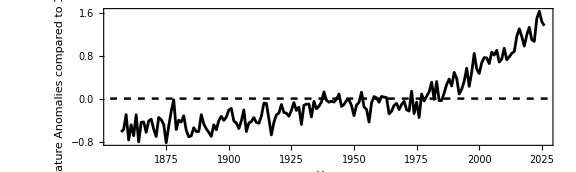

```mathematica
ListPlot[tempdata[[9;;,{1,2}]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Year",Black,16],Style["Temperature Anomalies\n compared to 1961-1990",Black,16]},AspectRatio->0.3,PlotStyle->Black,GridLines->{None, {0}},GridLinesStyle->Directive[Black, Dashed,Thickness[0.003]]]
```